```mathematica
ClearAll["`*"]
```

```mathematica
order = 3;
R = 10; Z=1; c = 137; k =-1
(*knot := Flatten[{0,0,0,Table[a,{a,1,9}],10,10,10}]*)
knot = Flatten[{0,0,0,Table[a,{a,0,2, 1/5}],3, 6, 9,12,15, 15, 15}]
n = Length[knot]-order-2
ϕi[r_, i_] := BSplineBasis[{order,knot},i, r]
v=-Z/r;
```

-1

{0,0,0,0,1/5,2/5,3/5,4/5,1,6/5,7/5,8/5,9/5,2,3,6,9,12,15,15,15}

16

```mathematica
Cmat =  Evaluate[Table[Integrate[ϕi[r,ai] ϕi[r,aj],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Cmat // Dimensions, SymmetricMatrixQ[Cmat]}
Cmat // MatrixForm
```

{{16,16},True}

```mathematica
Dmat =  Evaluate[Table[Integrate[ϕi[r,ai] D[ϕi[r,aj], r],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Dmat // Dimensions, SymmetricMatrixQ[Dmat]}
Dmat // MatrixForm
```

$Aborted

{{},False}

Dmat

```mathematica
Vmat = Evaluate[Table[Integrate[ϕi[r,ai] v ϕi[r,aj], {r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Vmat // Dimensions, SymmetricMatrixQ[Vmat]}
Vmat // MatrixForm
```

{{12,12},True}

(1/240 (2269-4860 Log[3/2]-135 Log[16]) | (-15371+35640 Log[3/2]+1080 Log[2])/1080 | (13807-33480 Log[3/2]-360 Log[2])/1440 | 1/432 (-1051+2592 Log[3/2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-15371+35640 Log[3/2]+1080 Log[2])/1080 | -2/27 (-737+3072 ArcCoth[7]+726 Log[3/2]+6 Log[2]) | 1/144 (-11885+33536 Log[4/3]+5456 Log[3/2]+16 Log[2]) | 1/90 (4959-16000 Log[4/3]-880 Log[3/2]) | (-29827+103680 Log[4/3])/2160 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(13807-33480 Log[3/2]-360 Log[2])/1440 | 1/144 (-11885+33536 Log[4/3]+5456 Log[3/2]+16 Log[2]) | 1/36 (8808-31250 ArcCoth[9]-17161 Log[4/3]-961 Log[3/2]-Log[2]) | 1/144 (-47173+142000 Log[5/4]+52400 Log[4/3]+992 Log[3/2]) | (334537-1271250 Log[5/4]-176850 Log[4/3])/1800 | (-35703+160000 Log[5/4])/1200 | 0 | 0 | 0 | 0 | 0 | 0
1/432 (-1051+2592 Log[3/2]) | 1/90 (4959-16000 Log[4/3]-880 Log[3/2]) | 1/144 (-47173+142000 Log[5/4]+52400 Log[4/3]+992 Log[3/2]) | -4/27 (-5513+24 ArcCoth[5]+15123 Log[5/4]+1875 Log[4/3]+8748 Log[2]+8748 Log[3]-8748 Log[5]) | (-16686371+46539360 Log[6/5]+34659360 Log[5/4]+1620000 Log[4/3])/21600 | -(2 (-204751+831060 Log[6/5]+238560 Log[5/4]))/1575 | (-295361+1620000 Log[6/5])/10080 | 0 | 0 | 0 | 0 | 0
0 | (-29827+103680 Log[4/3])/2160 | (334537-1271250 Log[5/4]-176850 Log[4/3])/1800 | (-16686371+46539360 Log[6/5]+34659360 Log[5/4]+1620000 Log[4/3])/21600 | 1/600 (585031-177147 ArcCoth[5]-1379052 ArcCoth[9]-4298427 ArcCoth[11]-12150 Log[4/3]) | (-11602319+44212392 Log[6/5]+5467392 Log[5/4]+5721192 Log[3/2])/25200 | (18296503-53865000 Log[6/5]-20907720 Log[3/2])/201600 | 3/640 (-1051+2592 Log[3/2]) | 0 | 0 | 0 | 0
0 | 0 | (-35703+160000 Log[5/4])/1200 | -(2 (-204751+831060 Log[6/5]+238560 Log[5/4]))/1575 | (-11602319+44212392 Log[6/5]+5467392 Log[5/4]+5721192 Log[3/2])/25200 | -(8 (-165998+320787 ArcCoth[5]+172800 ArcCoth[7]+37632 ArcCoth[9]+789507 ArcCoth[11]))/3675 | (-10015229+7695000 Log[6/5]+16704000 Log[4/3]+9378360 Log[3/2])/58800 | -(3 (-43151+125440 Log[4/3]+17440 Log[3/2]))/2800 | (-29827+103680 Log[4/3])/4200 | 0 | 0 | 0
0 | 0 | 0 | (-295361+1620000 Log[6/5])/10080 | (18296503-53865000 Log[6/5]-20907720 Log[3/2])/201600 | (-10015229+7695000 Log[6/5]+16704000 Log[4/3]+9378360 Log[3/2])/58800 | (26712959-20563560 ArcCoth[5]-5625000 ArcCoth[11]+60552000 Log[3]-49121280 Log[4]-11430720 Log[6])/141120 | (-2548289+4547200 Log[4/3]+3053920 Log[3/2])/22400 | (5777107-5637600 Log[4/3]-10251360 Log[3/2])/151200 | 1/216 (-1051+2592 Log[3/2]) | 0 | 0
0 | 0 | 0 | 0 | 3/640 (-1051+2592 Log[3/2]) | -(3 (-43151+125440 Log[4/3]+17440 Log[3/2]))/2800 | (-2548289+4547200 Log[4/3]+3053920 Log[3/2])/22400 | 1/200 (31353-80656 ArcCoth[5]-65536 ArcCoth[7]+200 Log[2]+19008 Log[3]-19208 Log[4]) | (-984799+2335776 Log[4/3]+770208 Log[3/2])/7200 | (124271-384000 Log[4/3]-34080 Log[3/2])/1800 | (-29827+103680 Log[4/3])/1800 | 0
0 | 0 | 0 | 0 | 0 | (-29827+103680 Log[4/3])/4200 | (5777107-5637600 Log[4/3]-10251360 Log[3/2])/151200 | (-984799+2335776 Log[4/3]+770208 Log[3/2])/7200 | (1543885-612912 ArcCoth[5]-6238524 ArcCoth[7]+2343750 Log[8]-2343750 Log[10])/5400 | (-1831123+5325000 Log[5/4]+2157000 Log[4/3]+54240 Log[3/2])/5400 | (3805831-14428125 Log[5/4]-2038365 Log[4/3])/18900 | 1/840 (-35703+160000 Log[5/4])
0 | 0 | 0 | 0 | 0 | 0 | 1/216 (-1051+2592 Log[3/2]) | (124271-384000 Log[4/3]-34080 Log[3/2])/1800 | (-1831123+5325000 Log[5/4]+2157000 Log[4/3]+54240 Log[3/2])/5400 | 1/360 (208963-1280 ArcCoth[5]-200000 ArcCoth[7]+806560 Log[8]-806560 Log[10]) | (-1544701+6556140 Log[5/4]+283500 Log[4/3])/3780 | (121673-545280 Log[5/4])/1260
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-29827+103680 Log[4/3])/1800 | (3805831-14428125 Log[5/4]-2038365 Log[4/3])/18900 | (-1544701+6556140 Log[5/4]+283500 Log[4/3])/3780 | (8080541+535815 Log[6]+34992000 Log[8]-35527815 Log[10])/26460 | (-1318807+5909760 Log[5/4])/17640
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/840 (-35703+160000 Log[5/4]) | (121673-545280 Log[5/4])/1260 | (-1318807+5909760 Log[5/4])/17640 | (27419+122880 Log[8]-122880 Log[10])/1470)

```mathematica
Kmat = Evaluate[Table[Integrate[ϕi[r,ai] k/r ϕi[r,aj],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Kmat // Dimensions, SymmetricMatrixQ[Kmat]}
Kmat // MatrixForm
```

{{12,12},True}

(1/240 (2269-4860 Log[3/2]-135 Log[16]) | (-15371+35640 Log[3/2]+1080 Log[2])/1080 | (13807-33480 Log[3/2]-360 Log[2])/1440 | 1/432 (-1051+2592 Log[3/2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-15371+35640 Log[3/2]+1080 Log[2])/1080 | -2/27 (-737+3072 ArcCoth[7]+726 Log[3/2]+6 Log[2]) | 1/144 (-11885+33536 Log[4/3]+5456 Log[3/2]+16 Log[2]) | 1/90 (4959-16000 Log[4/3]-880 Log[3/2]) | (-29827+103680 Log[4/3])/2160 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(13807-33480 Log[3/2]-360 Log[2])/1440 | 1/144 (-11885+33536 Log[4/3]+5456 Log[3/2]+16 Log[2]) | 1/36 (8808-31250 ArcCoth[9]-17161 Log[4/3]-961 Log[3/2]-Log[2]) | 1/144 (-47173+142000 Log[5/4]+52400 Log[4/3]+992 Log[3/2]) | (334537-1271250 Log[5/4]-176850 Log[4/3])/1800 | (-35703+160000 Log[5/4])/1200 | 0 | 0 | 0 | 0 | 0 | 0
1/432 (-1051+2592 Log[3/2]) | 1/90 (4959-16000 Log[4/3]-880 Log[3/2]) | 1/144 (-47173+142000 Log[5/4]+52400 Log[4/3]+992 Log[3/2]) | -4/27 (-5513+24 ArcCoth[5]+15123 Log[5/4]+1875 Log[4/3]+8748 Log[2]+8748 Log[3]-8748 Log[5]) | (-16686371+46539360 Log[6/5]+34659360 Log[5/4]+1620000 Log[4/3])/21600 | -(2 (-204751+831060 Log[6/5]+238560 Log[5/4]))/1575 | (-295361+1620000 Log[6/5])/10080 | 0 | 0 | 0 | 0 | 0
0 | (-29827+103680 Log[4/3])/2160 | (334537-1271250 Log[5/4]-176850 Log[4/3])/1800 | (-16686371+46539360 Log[6/5]+34659360 Log[5/4]+1620000 Log[4/3])/21600 | 1/600 (585031-177147 ArcCoth[5]-1379052 ArcCoth[9]-4298427 ArcCoth[11]-12150 Log[4/3]) | (-11602319+44212392 Log[6/5]+5467392 Log[5/4]+5721192 Log[3/2])/25200 | (18296503-53865000 Log[6/5]-20907720 Log[3/2])/201600 | 3/640 (-1051+2592 Log[3/2]) | 0 | 0 | 0 | 0
0 | 0 | (-35703+160000 Log[5/4])/1200 | -(2 (-204751+831060 Log[6/5]+238560 Log[5/4]))/1575 | (-11602319+44212392 Log[6/5]+5467392 Log[5/4]+5721192 Log[3/2])/25200 | -(8 (-165998+320787 ArcCoth[5]+172800 ArcCoth[7]+37632 ArcCoth[9]+789507 ArcCoth[11]))/3675 | (-10015229+7695000 Log[6/5]+16704000 Log[4/3]+9378360 Log[3/2])/58800 | -(3 (-43151+125440 Log[4/3]+17440 Log[3/2]))/2800 | (-29827+103680 Log[4/3])/4200 | 0 | 0 | 0
0 | 0 | 0 | (-295361+1620000 Log[6/5])/10080 | (18296503-53865000 Log[6/5]-20907720 Log[3/2])/201600 | (-10015229+7695000 Log[6/5]+16704000 Log[4/3]+9378360 Log[3/2])/58800 | (26712959-20563560 ArcCoth[5]-5625000 ArcCoth[11]+60552000 Log[3]-49121280 Log[4]-11430720 Log[6])/141120 | (-2548289+4547200 Log[4/3]+3053920 Log[3/2])/22400 | (5777107-5637600 Log[4/3]-10251360 Log[3/2])/151200 | 1/216 (-1051+2592 Log[3/2]) | 0 | 0
0 | 0 | 0 | 0 | 3/640 (-1051+2592 Log[3/2]) | -(3 (-43151+125440 Log[4/3]+17440 Log[3/2]))/2800 | (-2548289+4547200 Log[4/3]+3053920 Log[3/2])/22400 | 1/200 (31353-80656 ArcCoth[5]-65536 ArcCoth[7]+200 Log[2]+19008 Log[3]-19208 Log[4]) | (-984799+2335776 Log[4/3]+770208 Log[3/2])/7200 | (124271-384000 Log[4/3]-34080 Log[3/2])/1800 | (-29827+103680 Log[4/3])/1800 | 0
0 | 0 | 0 | 0 | 0 | (-29827+103680 Log[4/3])/4200 | (5777107-5637600 Log[4/3]-10251360 Log[3/2])/151200 | (-984799+2335776 Log[4/3]+770208 Log[3/2])/7200 | (1543885-612912 ArcCoth[5]-6238524 ArcCoth[7]+2343750 Log[8]-2343750 Log[10])/5400 | (-1831123+5325000 Log[5/4]+2157000 Log[4/3]+54240 Log[3/2])/5400 | (3805831-14428125 Log[5/4]-2038365 Log[4/3])/18900 | 1/840 (-35703+160000 Log[5/4])
0 | 0 | 0 | 0 | 0 | 0 | 1/216 (-1051+2592 Log[3/2]) | (124271-384000 Log[4/3]-34080 Log[3/2])/1800 | (-1831123+5325000 Log[5/4]+2157000 Log[4/3]+54240 Log[3/2])/5400 | 1/360 (208963-1280 ArcCoth[5]-200000 ArcCoth[7]+806560 Log[8]-806560 Log[10]) | (-1544701+6556140 Log[5/4]+283500 Log[4/3])/3780 | (121673-545280 Log[5/4])/1260
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-29827+103680 Log[4/3])/1800 | (3805831-14428125 Log[5/4]-2038365 Log[4/3])/18900 | (-1544701+6556140 Log[5/4]+283500 Log[4/3])/3780 | (8080541+535815 Log[6]+34992000 Log[8]-35527815 Log[10])/26460 | (-1318807+5909760 Log[5/4])/17640
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/840 (-35703+160000 Log[5/4]) | (121673-545280 Log[5/4])/1260 | (-1318807+5909760 Log[5/4])/17640 | (27419+122880 Log[8]-122880 Log[10])/1470)

```mathematica
Aprime = Table[If[k > 0, 
2 c^2 KroneckerDelta[i,1]KroneckerDelta[j,1]- c/2 KroneckerDelta[i,1]KroneckerDelta[j,n]- c/2 KroneckerDelta[i,n]KroneckerDelta[j,1]+ c/2 KroneckerDelta[i,n-1]KroneckerDelta[j,n-1]- c/2 KroneckerDelta[i,2n-2]KroneckerDelta[i,2n-2],
c KroneckerDelta[i,1]KroneckerDelta[j,1]- c/2 KroneckerDelta[i,1]KroneckerDelta[j,n]- c/2 KroneckerDelta[i,n]KroneckerDelta[j,1]+ c/2 KroneckerDelta[i,n-1]KroneckerDelta[j,n-1]- c/2 KroneckerDelta[i,2n-2]KroneckerDelta[j,2n-2]
],{i,1,2n-2},{j,1,2n-2}];
{Aprime // Dimensions, SymmetricMatrixQ[Aprime]}
Aprime // MatrixForm
```

{{24,24},True}

(137 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -137/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-137/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -137/2)

```mathematica
Amat = ArrayFlatten[{{Vmat, c (Dmat-Kmat)}, {-c(Dmat+Kmat), Vmat-2c^2 Cmat}}] + Aprime;
{Amat // Dimensions, SymmetricMatrixQ[Amat]}
N[Amat, 10] // MatrixForm
```

{{24,24},False}

(136.6839171 | -0.1589116593 | -0.01215611421 | -0.00007972172138 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -25.19663876 | 63.25145288 | 12.22580431 | 0.2011996536 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.1589116593 | -0.2523122115 | -0.09712523285 | -0.008027270708 | -0.00005681861081 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -19.70965823 | 34.56677298 | 59.92421246 | 11.75529164 | 0.1980619275 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.01215611421 | -0.09712523285 | -0.1631986306 | -0.06842867823 | -0.006007845159 | -0.0000264914387 | 0 | 0 | 0 | 0 | 0 | 0 | -8.89502902 | -33.31189866 | 22.35821239 | 55.99278447 | 11.55474145 | 0.1177959938 | 0 | 0 | 0 | 0 | 0 | 0
-0.00007972172138 | -0.008027270708 | -0.06842867823 | -0.1212403708 | -0.05485178501 | -0.00289344851 | -7.737479514×10^-6 | 0 | 0 | 0 | 0 | 0 | -0.1793559019 | -9.555819469 | -37.24332664 | 16.6099308 | 58.4140001 | 6.92021197 | 0.04183384422 | 0 | 0 | 0 | 0 | 0
0 | -0.00005681861081 | -0.006007845159 | -0.05485178501 | -0.148387499 | -0.06705797147 | -0.00792959723 | -0.0001614364858 | 0 | 0 | 0 | 0 | 0 | -0.1824936281 | -9.90859188 | -43.38461101 | 20.32908736 | 59.01253733 | 12.69669708 | 0.4074292986 | 0 | 0 | 0 | 0
0 | 0 | -0.0000264914387 | -0.00289344851 | -0.06705797147 | -0.1359251343 | -0.07186277141 | -0.00766141474 | -0.00002922099985 | 0 | 0 | 0 | 0 | 0 | -0.1105373396 | -6.127407078 | -40.63865315 | 18.6217434 | 56.08269968 | 11.17782811 | 0.1018604198 | 0 | 0 | 0
0 | 0 | 0 | -7.737479514×10^-6 | -0.00792959723 | -0.07186277141 | -0.1644443692 | -0.08406594614 | -0.008586258663 | -0.0001594434428 | 0 | 0 | 0 | 0 | 0 | -0.03971377483 | -10.52398744 | -36.39230032 | 22.52887858 | 58.02975784 | 12.17165474 | 0.4023993072 | 0 | 0
0 | 0 | 0 | 0 | -0.0001614364858 | -0.00766141474 | -0.08406594614 | -0.1612664958 | -0.07578465987 | -0.009537058783 | -0.00006818233297 | 0 | 0 | 0 | 0 | 0 | -0.3631957014 | -9.078600466 | -34.99568859 | 22.09350993 | 54.62208174 | 13.86491039 | 0.237674313 | 0
0 | 0 | 0 | 0 | 0 | -0.00002922099985 | -0.008586258663 | -0.07578465987 | -0.1334574524 | -0.06683916844 | -0.005985127963 | -0.00003784491243 | 0 | 0 | 0 | 0 | 0 | -0.09385386588 | -9.819019865 | -33.85708493 | 18.28367098 | 53.68196608 | 11.46464507 | 0.1682799911
0 | 0 | 0 | 0 | 0 | 0 | -0.0001594434428 | -0.009537058783 | -0.06683916844 | -0.1204657288 | -0.04835183777 | -0.0021552862 | 0 | 0 | 0 | 0 | 0 | 0 | -0.3587118039 | -11.25175628 | -35.36803392 | 18.40658262 | 55.98769384 | 6.492893257
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00006818233297 | -0.005985127963 | -0.04835183777 | -0.0531435822 | -0.004657947014 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.2189923537 | -9.824720009 | -26.97341727 | 39.93855058 | 12.45089384
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00003784491243 | -0.0021552862 | -0.004657947014 | 68.49940164 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.1579104851 | -2.640440076 | 2.338989081 | 1.479934158
-25.19663876 | -19.70965823 | -8.89502902 | -0.1793559019 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4089.276797 | -2810.543568 | -296.6914551 | -2.482751679 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
63.25145288 | 34.56677298 | -33.31189866 | -9.555819469 | -0.1824936281 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2810.543568 | -5998.387762 | -2956.959427 | -297.9286622 | -2.482728776 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12.22580431 | 59.92421246 | 22.35821239 | -37.24332664 | -9.90859188 | -0.1105373396 | 0 | 0 | 0 | 0 | 0 | 0 | -296.6914551 | -2956.959427 | -5998.298648 | -2956.93073 | -298.9197115 | -1.489629666 | 0 | 0 | 0 | 0 | 0 | 0
0.2011996536 | 11.75529164 | 55.99278447 | 16.6099308 | -43.38461101 | -6.127407078 | -0.03971377483 | 0 | 0 | 0 | 0 | 0 | -2.482751679 | -297.9286622 | -2956.93073 | -5998.25669 | -3076.333675 | -180.457678 | -0.5320088713 | 0 | 0 | 0 | 0 | 0
0 | 0.1980619275 | 11.55474145 | 58.4140001 | 20.32908736 | -40.63865315 | -10.52398744 | -0.3631957014 | 0 | 0 | 0 | 0 | 0 | -2.482728776 | -298.9197115 | -3076.333675 | -9679.589816 | -5022.370561 | -674.5055671 | -15.08239358 | 0 | 0 | 0 | 0
0 | 0 | 0.1177959938 | 6.92021197 | 59.01253733 | 18.6217434 | -36.39230032 | -9.078600466 | -0.09385386588 | 0 | 0 | 0 | 0 | 0 | -1.489629666 | -180.457678 | -5022.370561 | -11787.57865 | -7173.787951 | -856.1038859 | -3.830437384 | 0 | 0 | 0
0 | 0 | 0 | 0.04183384422 | 12.69669708 | 56.08269968 | 22.52887858 | -34.99568859 | -9.819019865 | -0.3587118039 | 0 | 0 | 0 | 0 | 0 | -0.5320088713 | -674.5055671 | -7173.787951 | -19638.1883 | -11737.65168 | -1412.045996 | -29.79222294 | 0 | 0
0 | 0 | 0 | 0 | 0.4074292986 | 11.17782811 | 58.02975784 | 22.09350993 | -33.85708493 | -11.25175628 | -0.2189923537 | 0 | 0 | 0 | 0 | 0 | -15.08239358 | -856.1038859 | -11737.65168 | -26786.20555 | -14767.25686 | -2127.16287 | -17.87530628 | 0
0 | 0 | 0 | 0 | 0 | 0.1018604198 | 12.17165474 | 54.62208174 | 18.28367098 | -35.36803392 | -9.824720009 | -0.1579104851 | 0 | 0 | 0 | 0 | 0 | -3.830437384 | -1412.045996 | -14767.25686 | -30322.49568 | -17386.71509 | -1786.678593 | -12.76806506
0 | 0 | 0 | 0 | 0 | 0 | 0.4023993072 | 13.86491039 | 53.68196608 | 14.60102706 | -42.73929029 | -5.902344838 | 0 | 0 | 0 | 0 | 0 | 0 | -29.79222294 | -2127.16287 | -17386.71509 | -35691.01253 | -15947.31434 | -766.0837879
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.237674313 | 11.46464507 | 40.22182082 | -25.37720906 | -11.17461636 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -17.87530628 | -1786.678593 | -15947.31434 | -18549.56468 | -1683.560246
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1682799911 | 3.230988495 | -1.062711599 | -1.315984209 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12.76806506 | -766.0837879 | -1683.560246 | -287.3810648)

```mathematica
Bmat = ArrayFlatten[{{Cmat,0}, {0,Cmat}}];
{Bmat // Dimensions, SymmetricMatrixQ[Bmat]}
```

{{24,24},True}

```mathematica
energy = Eigenvalues[N[{Amat, Bmat},30]]
```

{-108790.128099347117144425249268,71251.9282234902514733373322081,-37567.3531512479760036071275289,-37551.0606471536127521097255889,-37546.7063518455780626918762661,-37541.9818647619850809869804611,-37540.933687345243035146703418,-37539.8018970306612477466310924,-37539.2060136448956195706977497,-37538.8055615302854558279416903,-37538.5682835033735549232425762,-37538.3573633487660505091731203,-37538.1954850632955251729185305,2133.29276308202272566705694169,13.8868249568036237290395018276,9.97508090934964158065053295881,4.0046276477559290576107009076,2.05748990836421397002928668056,0.833328811627564326898750089991,0.504623342434178175543733256322,-0.326478985754657957307098665382,0.236156670179378771804950914487,-0.0946098330819262584762642066311,0.0493562800300135551152257064778}

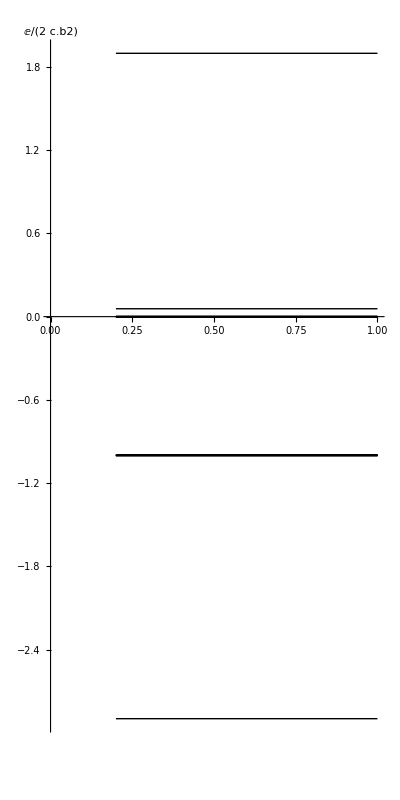

```mathematica
Plot[energy/(2 c^2),{x,.2,1},PlotStyle->{{Thin, Black}},Axes->{False,True},AspectRatio->2,PlotRange->{{0,1},Automatic}, AxesLabel->E/(2 c.b2)]
```